Wigner in Fock basis. For nm the Wigner is denoted by W[n,m]

```mathematica
ℏ=1;
(* Wigner of nm. Ref: StackExchange answer to "What is the Winger of nm?" by Cosmas Zachos. *)
W[m_,n_,q_,p_]:=lim_(x->q) ((-1)^Min[m,n]/π √(((Min[m,n])!)/((Max[m,n])!))ⅇ^(-(q^2+p^2))(√2(x+Sign[m-n]ⅈ p))^Abs[m-n] LaguerreL[Min[n,m],Abs[m-n],2(q^2+p^2)]);
```

```mathematica
(* Options for the density plot *)
cols=RGBColor/@{"#053061","#2166ac","#4393c3","#92c5de","#d1e5f0","#f7f7f7","#fddbc7","#f4a582","#d6604d","#b2182b","#67001f"};
limits=3.5;
range=35;
n=1;
m=1;
(* Construct matrix to plot *)
mat=Table[Re[Chop[W[n,m,(q-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{q,1,2 range +1}];
(* Normalize the mat *)
mat=mat/((*Abs[ Total[mat,2]](limits/range)^2*)1);
(* Plot *)
ListDensityPlot[mat,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->(Blend[Reverse[cols],(#/Max[{Abs[Max[mat]],Abs[Min[mat]]}]+1)/2]&),ColorFunctionScaling->False,PlotRange->All,FrameLabel->{"q (in units of √ℏ)","p (in units of √ℏ)"},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium,InterpolationOrder->2]
```

-Graphics-

#### THRESHOLD DETECTOR

```mathematica
(* OUTPUT STATE after for ideal k photon subtraction for various inputs *)
(* Plus state input to the beamsplitter *)
ρkTilde[1][n_,m_,N_,K_,k_,t_]:=UnitStep[n]UnitStep[m]UnitStep[kmax[1][N,K]-n]UnitStep[kmax[1][N,K]-m]Mod[n+k,N]Mod[m+k,N] 1/2^K √(Binomial[K,(n+k)/N]Binomial[K,(m+k)/N]Binomial[n +k, k]Binomial[m +k, k])lim_(tL->t) (tL^(n +m)(1-tL^2)^k);(* unnormalized density matrix in the Fock basis *)

WkTilde[1][N_,K_,k_,q_,p_,t_]:=∑_(n=⌈k/N⌉)^K ∑_(m=⌈k/N⌉)^K (1/2^K √(Binomial[K,n]Binomial[K,m]Binomial[n N, k]Binomial[m N, k])lim_(tL->t) (tL^(n N+ m N - 2 k)(1-tL^2)^k)W[n N-k,m N-k,q,p]);
kmax[1][N_,K_]:=K N;
probk[1][N_,K_,k_,t_]:= ∑_(n=⌈k/N⌉)^K ((Binomial[K,n]Binomial[n N, k])/2^K lim_(tL->t) (tL^(2 n N - 2 k)(1-tL^2)^k));
(* Minus state input *)
ρkTilde[2][n_,m_,N_,K_,k_,t_]:=UnitStep[n]UnitStep[m]UnitStep[kmax[2][N,K]-n]UnitStep[kmax[2][N,K]-m]Mod[n+k,N]Mod[m+k,N] 1/2^K √(Binomial[K,(n+k)/N]Binomial[K,(m+k)/N]Binomial[n +k, k]Binomial[m +k, k])lim_(tL->t) (tL^(n +m)(1-tL^2)^k)(-1)^((n+m+2k)/N);

WkTilde[2][N_,K_,k_,q_,p_,t_]:=∑_(n=⌈k/N⌉)^K ∑_(m=⌈k/N⌉)^K (1/2^K √(Binomial[K,n]Binomial[K,m]Binomial[n N, k]Binomial[m N, k])lim_(tL->t) (tL^(n N+ m N - 2k)(1-tL^2)^k)(-1)^(n+m)W[n N-k,m N-k,q,p]);
kmax[2][N_,K_]:= K N;
probk[2][N_,K_,k_,t_]:=∑_(n=⌈k/N⌉)^K ((Binomial[K,n]Binomial[n N, k])/2^K lim_(tL->t) (tL^(2 n N - 2k)(1-tL^2)^k));
(* Zero state input *)
ρkTilde[3][n_,m_,N_,K_,k_,t_]:=UnitStep[n]UnitStep[m]UnitStep[kmax[3][N,K]-n]UnitStep[kmax[3][N,K]-m]Mod[n+k,2N]Mod[m+k,2N] 1/2^(K-1)√(Binomial[K,(n+k)/N]Binomial[K,(m+k)/N]Binomial[n +k, k]Binomial[m +k, k])lim_(tL->t) (tL^(n +m)(1-tL^2)^k);

WkTilde[3][N_,K_,k_,q_,p_,t_]:=∑_(n=⌈k/(2N)⌉)^⌊K/2⌋ ∑_(m=⌈k/(2N)⌉)^⌊K/2⌋ (1/2^(K-1)√(Binomial[K,2n]Binomial[K,2m]Binomial[2n N, k]Binomial[2m N, k])lim_(tL->t) (tL^(2n N+ 2m N - 2k)(1-tL^2)^k)W[2n N-k,2m N-k,q,p]);
kmax[3][N_,K_]:=2⌊K/2⌋N;
probk[3][N_,K_,k_,t_]:=∑_(n=⌈k/(2N)⌉)^⌊K/2⌋ ((Binomial[K,2n]Binomial[2n N, k])/2^(K-1)lim_(tL->t) (tL^(4n N - 2k)(1-tL^2)^k));

(* One state input *)
ρkTilde[4][n_,m_,N_,K_,k_,t_]:=UnitStep[n]UnitStep[m]UnitStep[kmax[4][N,K]-n]UnitStep[kmax[4][N,K]-m]Mod[n+k-N,2N]Mod[m+k-N,2N] 1/2^(K-1)√(Binomial[K,(n+k)/N]Binomial[K,(m+k)/N]Binomial[n +k, k]Binomial[m +k, k])lim_(tL->t) (tL^(n +m)(1-tL^2)^k);

WkTilde[4][N_,K_,k_,q_,p_,t_]:=∑_(n=⌈(k/N-1)/2⌉)^⌊(K-1)/2⌋ ∑_(m=⌈(k/N-1)/2⌉)^⌊(K-1)/2⌋ (1/2^(K-1)√(Binomial[K,(2n+1)]Binomial[K,(2m+1)]Binomial[(2n+1) N, k]Binomial[(2m+1) N, k])lim_(tL->t) (tL^((2n+1) N+ (2m+1) N - 2k)(1-tL^2)^k)W[(2n +1)N-k,(2m+1) N-k,q,p]);
kmax[4][N_,K_]:=(2⌊(K-1)/2⌋+1)N;
probk[4][N_,K_,k_,t_]:=∑_(n=⌈(k/N-1)/2⌉)^⌊(K-1)/2⌋ ((Binomial[K,(2n+1)]Binomial[(2n+1) N, k])/2^(K-1)lim_(tL->t) (tL^(2(2n+1) N- 2k)(1-tL^2)^k));

(* Normalized states *)
Wk[j_,N_,K_,k_,q_,p_,t_]:=(WkTilde[j][N,K,k,q,p,t])/(probk[j][N,K,k,t]);

(* Ideal binomial codewords (no beamsplitting or detections involved) *)
Wbc[1][N_,K_,q_,p_]:=∑_(n=0)^K ∑_(m=0)^K (1/2^K √(Binomial[K,n]Binomial[K,m])W[n N,m N,q,p]);
Wbc[2][N_,K_,q_,p_]:=∑_(n=0)^K ∑_(m=0)^K (1/2^K √(Binomial[K,n]Binomial[K,m])(-1)^(n+m)W[n N,m N,q,p]);
Wbc[3][N_,K_,q_,p_]:=∑_(n=0)^⌊K/2⌋ ∑_(m=0)^⌊K/2⌋ (1/2^(K-1)√(Binomial[K,2n]Binomial[K,2m])W[2n N,2m N,q,p]);
Wbc[4][N_,K_,q_,p_]:=∑_(n=0)^⌊(K-1)/2⌋ ∑_(m=0)^⌊(K-1)/2⌋ (1/2^(K-1)√(Binomial[K,(2n+1)]Binomial[K,(2m+1)])W[(2n +1)N,(2m+1) N,q,p]);
```

```mathematica
(* Normalized OUTPUT STATE after inefficient no-click event *)
WoutTilde[j_,N_,K_,q_,p_,t_,η_]:=∑_(k=0)^(kmax[j][N,K]) (WkTilde[j][N,K,k,q,p,t]lim_(ηL->η) ((1-ηL)^k));
prout[j_,N_,K_,t_,η_]:=∑_(k=0)^(kmax[j][N,K]) (probk[j][N,K,k,t]lim_(ηL->η) ((1-ηL)^k)); (* probability of no-click *)
Wout[j_,N_,K_,q_,p_,t_,η_]:= WoutTilde[j,N,K,q,p,t,η]/prout[j,N,K,t,η];


Fidelity[j_,N_,K_,t_,η_]:=(∑_(k=0)^(kmax[j][N,K]) (lim_(ηL->η) ((1-ηL)^k)overlap[j,k,0,N,K,t]))/(prout[j,N,K,t,η]probk[j][N,K,0,t]);
overlap[j_,k_,l_,N_,K_,t_]:=∑_(n=0)^(kmax[j][N,K]-k) ∑_(m=0)^(kmax[j][N,K]-k) ρkTilde[j][n,m,N,K,k,t]ρkTilde[j][m,n,N,K,l,t];
(* overlap[j_,k_,l_,N_,K_,t_]:= 2π∫_(-∞)^∞ (∫_(-∞)^∞ WkTilde[j][N,K,k,q,p,t]WkTilde[j][N,K,l,q,p,t]ⅆp)ⅆq; *)
```

```mathematica
(* Options for the density plot *)
cols=RGBColor/@{"#053061","#2166ac","#4393c3","#92c5de","#d1e5f0","#f7f7f7","#fddbc7","#f4a582","#d6604d","#b2182b","#67001f"};
limits=3.5;
range=35;
Num=2;
K=3;
η=1;
t=√(.98);
(* Construct matrix to plot *)
mat=Table[Re[Chop[WoutTilde[3,Num,K,(q-1)(limits/range)-limits,(p-1)(limits/range)-limits,t,η]]],{p,1,2 range +1},{q,1,2 range +1}];
(* Normalize the mat *)
mat=mat/(Abs[ Total[mat,2]](limits/range)^2);
(* Plot *)
ListDensityPlot[mat,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->(Blend[Reverse[cols],(#/Max[{Abs[Max[mat]],Abs[Min[mat]]}]+1)/2]&),ColorFunctionScaling->False,PlotRange->Full,FrameLabel->{"q (in units of √ℏ)","p (in units of √ℏ)"},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium,PlotLegends->Automatic,InterpolationOrder->2]
```

-Graphics-

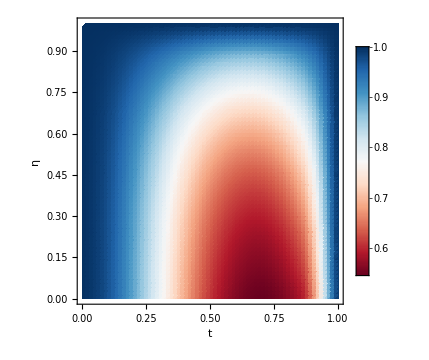

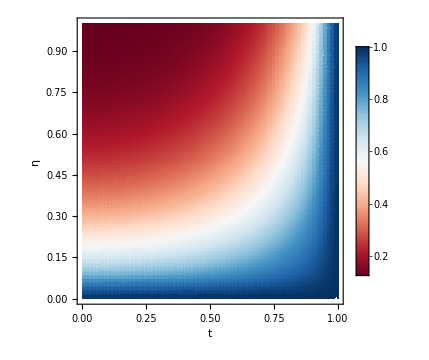

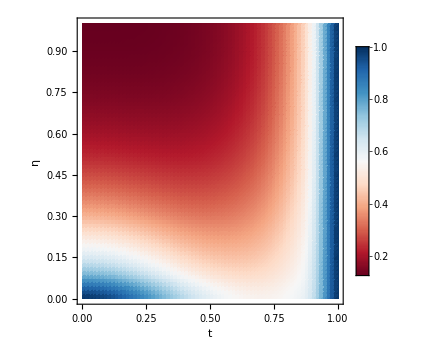

```mathematica
cols=RGBColor/@{"#053061","#2166ac","#4393c3","#92c5de","#d1e5f0","#f7f7f7","#fddbc7","#f4a582","#d6604d","#b2182b","#67001f"};
limitx=1;
limity= 1;
rangex = 10;
rangey = 10;
mat=Table[Fidelity[1,2,3,t(limitx/rangex),η(limity/rangey)],{η,0, rangey }(* y-axis *),{t,0, rangex}(* x-axis *)];
ListDensityPlot[mat,DataRange->{{0,limitx},{0,limity}},ColorFunction->(Blend[Reverse[cols],#]&),ColorFunctionScaling->True,PlotRange->All,FrameLabel->{"t","η","Fidelity"},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},ImageSize->Medium,PlotLegends->Automatic,InterpolationOrder->2]
ClearAll[mat];
mat=Table[prout[1,2,3,t(limitx/rangex),η(limity/rangey)],{η,0, rangey }(* y-axis *),{t,0, rangex}(* x-axis *)];
ListDensityPlot[mat,DataRange->{{0,limitx},{0,limity}},ColorFunction->(Blend[Reverse[cols],#]&),ColorFunctionScaling->True,PlotRange->All,FrameLabel->{"t","η","Success probability"},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},ImageSize->Medium,PlotLegends->Automatic,InterpolationOrder->2]
ClearAll[mat];
mat=Table[Fidelity[1,2,3,t(limitx/rangex),η(limity/rangey)]prout[1,2,3,t(limitx/rangex),η(limity/rangey)],{η,0, rangey }(* y-axis *),{t,0, rangex}(* x-axis *)];
ListDensityPlot[mat,DataRange->{{0,limitx},{0,limity}},ColorFunction->(Blend[Reverse[cols],#]&),ColorFunctionScaling->True,PlotRange->All,FrameLabel->{"t","η","Fidelity x Success probability"},LabelStyle->{FontSize->Large,FontFamily->"Arial",Black},ImageSize->Medium,PlotLegends->Automatic,InterpolationOrder->2]
ClearAll[mat];
```